```mathematica
eq1=x^2+x-2==0;
Solve[eq1]
```

{{x→-2},{x→1}}

```mathematica
Clear["Global`*"]  (*清除所有全局变量*)
Solve[{x^2+y^2==2,y==x^2+x-2},{x,y},Assumptions->{{x,y} ∈ Reals}]//N
Reduce[{x^2+y^2==2,y==x^2+x-2,x∈Reals},{x,y}]//N
```

{{x→0.454334,y→-1.33925},{x→1.22133,y→0.712985}}

(x==0.454334||x==1.22133)&&y==-2.+x+x^2

```mathematica
Eliminate[{a x+y==0,2 x+(1-a) y==1},y]
```

-1+2 x-a x+a^2 x==0

```mathematica
x=4
x^2+3 x==2
Clear["Global`*"]
x^2+3 x==2
```

4

False

3 x+x^2==2

```mathematica
Table[Table[i^2,{i,1,10,k}],{k,1,2,1}]
```

{{1,4,9,16,25,36,49,64,81,100},{1,9,25,49,81}}

```mathematica
sol=Reduce[{(1-x)/x^2==(T)^(3/2)Exp[1/T],T∈PositiveReals,x>0},x]/.T->1//N
sol[[2]]
```

x==0.449869

0.449869

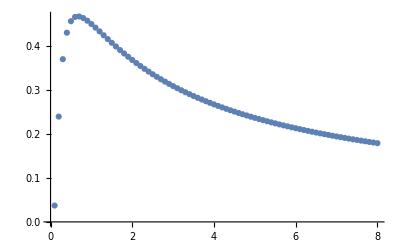

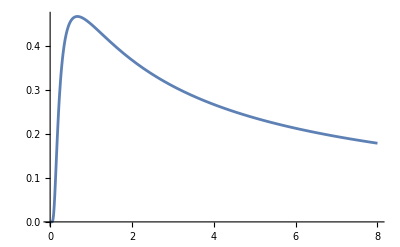

```mathematica
Table[{T,Reduce[{(1-x)/x^2==(T)^(3/2)Exp[1/T],T∈PositiveReals,x>0},x][[2]]//N},{T,0.1,8,0.1}];
ListPlot[%]
Plot[Reduce[{(1-x)/x^2==(T)^(3/2)Exp[1/T],T∈PositiveReals,x>0},x][[2]]//N,{T,0.01,8}]
```

Reduce  可以发现在什么参数条件下方程组有解 . 而  Solve  则告诉用户是否存在通解 .

```mathematica
Reduce[a x^2+b x+c==0,x]
```

(a≠0&&(x==(-b-√(b^2-4 a c))/(2 a)||x==(-b+√(b^2-4 a c))/(2 a)))||(a==0&&b≠0&&x==-c/b)||(c==0&&b==0&&a==0)

```mathematica
Reduce[{Sin[x]==1/2},x]
```

C[1]∈ℤ&&(x==π/6+2 π C[1]||x==(5 π)/6+2 π C[1])

```mathematica
Clear["Global`*"]
cont1=A  Exp[-I κ a/2]+B Exp[I κ a/2]==X  Exp[-I k a/2]+Y Exp[I k a/2];
dcont1=A  κ Exp[-I κ a/2]-B κ Exp[I κ a/2]==X  k Exp[-I k a/2]- Y k Exp[I k a/2];
cont2=X  Exp[I k a/2]+Y Exp[-I k a/2]==F Exp[I κ a/2];
dcont2=X  k Exp[I k a/2]- Y k Exp[-I k a/2]==F κ Exp[I κ a/2];
Solve[{cont1,dcont1,cont2,dcont2},{B,X,Y,F}]//FullSimplify
```

{{B→(A ⅇ^(-ⅈ a κ) (-1+ⅇ^(2 ⅈ a k)) (-k^2+κ^2))/(ⅇ^(2 ⅈ a k) (k-κ)^2-(k+κ)^2),X→-(2 A ⅇ^(1/2 ⅈ a (k-κ)) κ (k+κ))/(ⅇ^(2 ⅈ a k) (k-κ)^2-(k+κ)^2),Y→-(2 A ⅇ^(1/2 ⅈ a (3 k-κ)) (k-κ) κ)/(ⅇ^(2 ⅈ a k) (k-κ)^2-(k+κ)^2),F→-(4 A ⅇ^(ⅈ a (k-κ)) k κ)/(ⅇ^(2 ⅈ a k) (k-κ)^2-(k+κ)^2)}}

```mathematica
T=FullSimplify[Conjugate[(4 ⅇ^(ⅈ a (k-κ)) k κ)/(ⅇ^(2 ⅈ a k) (k-κ)^2-(k+κ)^2)](4 ⅇ^(ⅈ a (k-κ)) k κ)/(ⅇ^(2 ⅈ a k) (k-κ)^2-(k+κ)^2),k∈Reals&&κ∈Reals&&a∈Reals]
R=FullSimplify[Conjugate[(ⅇ^(-ⅈ a κ) (-1+ⅇ^(2 ⅈ a k)) (-k^2+κ^2))/(ⅇ^(2 ⅈ a k) (k-κ)^2-(k+κ)^2)](ⅇ^(-ⅈ a κ) (-1+ⅇ^(2 ⅈ a k)) (-k^2+κ^2))/(ⅇ^(2 ⅈ a k) (k-κ)^2-(k+κ)^2),k∈Reals&&κ∈Reals&&a∈Reals]
Simplify[R+T]
```

(8 k^2 κ^2)/(k^4+6 k^2 κ^2+κ^4-(k^2-κ^2)^2 Cos[2 a k])

(2 (k-κ)^2 (k+κ)^2 Sin[a k]^2)/(k^4+6 k^2 κ^2+κ^4-(k^2-κ^2)^2 Cos[2 a k])

1